## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

169

Test Legend fuctioning.

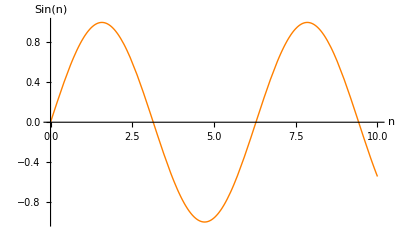

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=31 ;tranzDE2=29;tranzDE3=23;tranzDE4=23;tranzL=23;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
norts=200-tranzs;nortL=200-tranzL;nort2=200-tranzDE2;nort3=200-tranzDE4;nort4=200-tranzDE4;
nort=200-tranzs
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",30,Bold,Orange]]
(*********************************************)
w1 =-1;
w2 =-0.1;
w3 =-0.5;
w4 =-4/5;
ΩDE0 =0.73;
Ωk0=0;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
h=0.71;
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h;(*the real value is not very important here. this means all length units are MPc/h, all wavenumber units are h/MPc*)
Ωm0s =1; 
Ωr0s =8.09*10^-5;
(*Ωr0s=0;*)
nzs=nzL=nz2=nz3=nz4=aeq=Ωr0/Ωm0
c=300000
```

Parameters

0.00029963

300000

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",30,Bold,Orange]]
(*********************************************)
HL0=H20=H30=H40=H0;
Hs0=H0;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",30,Bold,Orange]]
(*********************************************)
Hs[a_]:= Hs0  √(Ωr0s a^-4+Ωm0s a^-3);
HL[a_]:= HL0  √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w1)))
H2[a_]:= H20 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w2)))
H3[a_]:= H30 √(Ωr0 a^-4+ Ωm0 a^-3+ ΩDE0 a^(-3(1+w3)))
H4[a_]:= H40 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w4)))
(*For integral*)
iHs[a_]:= Hs0  √(Ωm0s a^-1);
iHL[a_]:= HL0  √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w1)+2))
iH2[a_]:= H20 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w2)+2))
iH3[a_]:= H30 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w3)+2))
iH4[a_]:= H40 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w4)+2))
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Particle Horizon",30,Bold,Orange]]
(*********************************************)
dHs[a_?NumberQ]:=c a NIntegrate[1/(Hs[x] x^2),{x,0,a}];
dHL[a_?NumberQ]:=c a NIntegrate[1/(HL[x] x^2),{x,0,a}];
dH2[a_?NumberQ]:=c a NIntegrate[1/(H2[x] x^2),{x,0,a}];
dH3[a_?NumberQ]:=c a NIntegrate[1/(H3[x] x^2),{x,0,a}];dH4[a_?NumberQ]:=c a NIntegrate[1/(H4[x] x^2),{x,0,a}];
```

Particle Horizon

```mathematica
(*********************************************)
Print[Style["Define k of a",30,Bold,Orange]]
(*********************************************)
kL[a_]:= 1/dHL[a];ks[a_]:= 1/dHs[a];kDE2[a_]:= 1/dH2[a];kDE3[a_]:= 1/dH3[a];kDE4[a_]:= 1/dH4[a];
1/dHL[0.01]
{keqL=1/dHL[aeq],keq2=1/dH2[aeq],keq3=1/dH3[aeq],keq4=1/dH4[aeq]}
{k0L=1/dHL[1],k02=1/dH2[1],k03=1/dH3[1],k04=1/dH4[1]}
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

0.0730456

{28.6212,29.4329,28.6212,28.6212}

{0.0000699507,0.000100025,0.0000761142,0.0000715993}

```mathematica
(*********************************************)
Print[Style["The equation for growth factors",30,Bold,Orange]]
(*********************************************)
(*
DGG2=D[D[GG2[a],a],a]+(5/a+D[iH2[a],a]/iH2[a])D[GG2[a],a]+1/a(3/(2 a)+D[iH2[a],a]/iH2[a])(1-1/w2)GG2[a]==0
DGG3=D[D[GG3[a],a],a]+(5/a+D[iH3[a],a]/iH3[a])D[GG3[a],a]+1/a(3/(2 a)+D[iH3[a],a]/iH3[a])(1-1/w3)GG3[a]==0
DGG4=D[D[GG4[a],a],a]+(5/a+D[iH4[a],a]/iH4[a])D[GG4[a],a]+1/a(3/(2 a)+D[iH4[a],a]/iH4[a])(1-1/w4)GG4[a]==0
*)
(*
DGG2=a^2×∂_(a,a) GG2[a]+3/2×a×(1-w2×H2[a]^-2×H20^2×ΩDE0×a^(-3×(1+w2)))×∂_a GG2[a]-3/2×H2[a]^-2×H20^2×Ωm0 a^-3×GG2[a]==0
DGG3=a^2×∂_(a,a) GG3[a]+3/2×a×(1-w3×H3[a]^-2×H30^2×ΩDE0×a^(-3×(1+w3)))×∂_a GG3[a]-3/2×H3[a]^-2×H30^2×Ωm0 a^-3×GG3[a]==0
DGG4=a^2×∂_(a,a) GG4[a]+3/2×a×(1-w4×H4[a]^-2×H40^2×ΩDE0×a^(-3×(1+w4)))×∂_a GG4[a]-3/2×H4[a]^-2×H40^2×Ωm0 a^-3×GG4[a]==0
*)
```

The equation for growth factors

Define growth factors

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. The computed solution may match the boundary conditions poorly.

{{DgL→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg3→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg2→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg4→InterpolatingFunction[{{0.001,10000.}},<>]}}

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

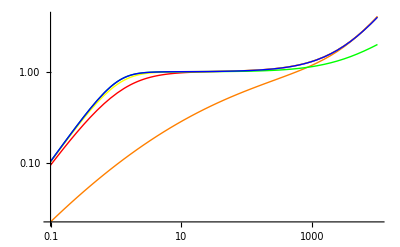

```mathematica
(*********************************************)
Print[Style["Define growth factors",30,Bold,Orange]]
(*********************************************)
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
(*
solL=NDSolve[{DgL''[a]+(3/a+HL'[a]/HL[a])DgL'[a]+HL'[a]/(a HL[a])DgL[a]==0,DgL[10^-2]==N[Growths[10^-2]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10000}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
sol2=NDSolve[{Dg2''[a]+(3/a+H2'[a]/H2[a])Dg2'[a]-(3/2(1+1/w2)1/a^2+1/w2 H2'[a]/(a H2[a]))Dg2[a]==0,Dg2[10^-5]==N[GrowthL2[10^-5]],Dg2'[10^-5]==N[GrowthL2'[10^-5]]},Dg2,{a,0.001,10000}]
sol3=NDSolve[{Dg3''[a]+(3/a+H3'[a]/H3[a])Dg3'[a]-(3/2(1+1/w3)1/a^2+1/w3 H3'[a]/(a H3[a]))Dg3[a]==0,Dg3[10^-5]==N[GrowthL2[10^-5]],Dg3'[10^-5]==N[GrowthL2'[10^-5]]},Dg3,{a,0.001,10000}]
sol4=NDSolve[{Dg4''[a]+(3/a+H4'[a]/H4[a])Dg4'[a]-(3/2(1+1/w4)1/a^2+1/w4 H4'[a]/(a H4[a]))Dg4[a]==0,Dg4[10^-5]==N[GrowthL2[10^-5]],Dg4'[10^-5]==N[GrowthL2'[10^-5]]},Dg4,{a,0.001,10000}]
*)
solL=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-9]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10000}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
sol3=NDSolve[{a^2×D[Dg3[a], a,a]+3/2×a×(1-w3×H3[a]^-2×H30^2×ΩDE0×a^(-3×(1+w3)))×D[Dg3[a], a]-3/2×H3[a]^-2×H30^2×Ωm0 a^-3×Dg3[a]==0,Dg3[10^-7]==N[GrowthL2[10^-7]],Dg3'[10^-7]==N[GrowthL2'[10^-7]]},Dg3,{a,0.001,10000}]
sol2=NDSolve[{a^2×D[Dg2[a], a,a]+3/2×a×(1-w2×H2[a]^-2×H20^2×ΩDE0×a^(-3×(1+w2)))×D[Dg2[a], a]-3/2×H2[a]^-2×H20^2×Ωm0 a^-3×Dg2[a]==0,Dg2[10^-7]==N[GrowthL2[10^-7]],Dg2'[10^-7]==N[GrowthL2'[10^-7]]},Dg2,{a,0.001,10000}]
sol4=NDSolve[{a^2×D[Dg4[a], a,a]+3/2×a×(1-w4×H4[a]^-2×H40^2×ΩDE0×a^(-3×(1+w4)))×D[Dg4[a], a]-3/2×H4[a]^-2×H40^2×Ωm0 a^-3×Dg4[a]==0,Dg4[10^-7]==N[GrowthL2[10^-7]],Dg4'[10^-7]==N[GrowthL2'[10^-7]]},Dg4,{a,0.001,10000}]
GrowthDE2[a_]:=Dg2[a]/.sol2[[1]]
GrowthDE3[a_]:=Dg3[a]/.sol3[[1]]
GrowthDE4[a_]:=Dg4[a]/.sol4[[1]]
LogLogPlot[{mn GrowthDE3[1/mn],mn GrowthDE2[1/mn],mn GrowthDE4[1/mn],mn GrowthL[1/mn],mn GrowthL2[1/mn]},{mn,0.1,10000},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
(*
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
s2=NDSolve[{DGG2,,GG2[0.00001]==N[GrowthL[0.00001]],GG2'[0.00001]==N[GrowthL'[0.00001]]},GG2,{a,0.00001,1000}]
s3=NDSolve[{DGG3,,GG3[0.00001]==N[GrowthL[0.00001]],GG3'[0.00001]==N[GrowthL'[0.00001]]},GG3,{a,0.00001,1000}]
s4=NDSolve[{DGG4,,GG4[0.00001]==N[GrowthL[0.00001]],GG4'[0.00001]==N[GrowthL'[0.00001]]},GG4,{a,0.00001,1000}]
LogLogPlot[{Evaluate[GG2[a]/.s2],Evaluate[GG3[a]/.s3],Evaluate[GG4[a]/.s4],GrowthL[a]},{a,0.1,1000},PlotRange->{{0.1,1000},{0.1,1.1}},PlotStyle->{Red,Orange,Yellow,Green}]
(*
GrowthDE2[a_]:=5/2 Ωm0  H2[a]/H20  NIntegrate[1/(iH2[x]/H20)^3,{x,0,a}];
GrowthDE3[a_]:=5/2 Ωm0  H3[a]/H30  NIntegrate[1/(iH3[x]/H30)^3,{x,0,a}];
GrowthDE4[a_]:=5/2 Ωm0  H4[a]/H40  NIntegrate[1/(iH4[x]/H40)^3,{x,0,a}];
*)
*)
```

Plot k of a

0.000119402

0.0000699507

0.000100025

0.0000761142

0.0000715993

28.5557

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0000862641}. NIntegrate obtained -0.00024017 + 0.00912658\ ⅈ and 0.0000301288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000898138 + 0.0175416\ ⅈ and 0.0000957909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.00110296 + 0.0175295\ ⅈ and 0.0000957045 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

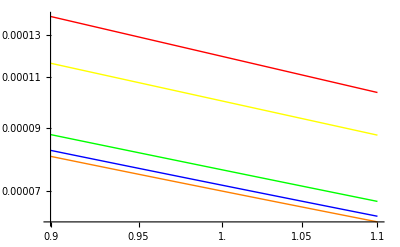

```mathematica
(*********************************************)
Print[Style["Plot k of a",30,Bold,Orange]]
(*********************************************)
ks[1]
kL[1]
kDE2[1]
kDE3[1]
kDE4[1]
kL[3*10^-4]
LogLogPlot[{ks[a],kL[a],kDE2[a],kDE3[a],kDE4[a]},{a,0.9,1.1},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
```

Plot growth factors of a for LCDM

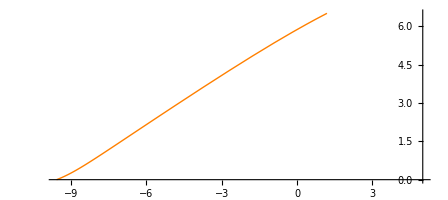

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",30,Bold,Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Orange}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

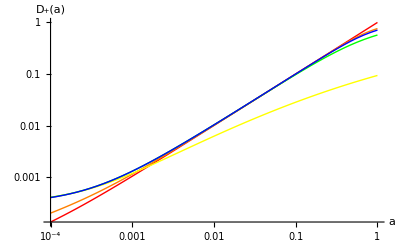

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
(*Plot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,0.0000001,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]*)
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

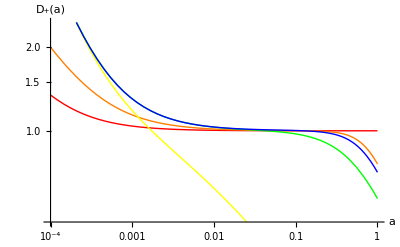

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
(*Plot[{Growths[a]/a,GrowthL[a]/a,GrowthDE2[a]/a,GrowthDE3[a]/a,GrowthDE4[a]/a},{a,0.0000001,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]*)
LogLogPlot[{Growths[a]/a,GrowthL[a]/a,GrowthDE2[a]/a,GrowthDE3[a]/a,GrowthDE4[a]/a},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",30,Bold,Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];GDE4:=GrowthDE4[1/mn];
(*
GS[mn_]:=Growths[1/mn]/(nzs  Growths[1/nzs]);GL[mn_]:=GrowthL[1/mn]/(nzL GrowthL[1/nzL]);GDE2[mn_]:=GrowthDE2[1/mn]/(nz2 GrowthDE2[1/nz2]);GDE3[mn_]:=GrowthDE3[1/mn]/(nz3 GrowthDE3[1/nz3]);GDE4[mn_]:=GrowthDE4[1/mn]/(nz4 GrowthDE4[1/nz4]);
*)
(*
GS1[mn_]= 5/2 Ωm0s  Hs[1]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,1}];
GL1[mn_]= 5/2 Ωm0  HL[1]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,1}];
G21[mn_]=5/2 Ωm0  H2[1]/H20  NIntegrate[1/(iH2[x]/H20)^3,{x,0,1}];
G31[mn_]=5/2 Ωm0  H3[1]/H30  NIntegrate[1/(iH3[x]/H30)^3,{x,0,1}];
G41[mn_]=5/2 Ωm0  H4[1]/H40  NIntegrate[1/(iH4[x]/H40)^3,{x,0,1}];
*)
Lambdas[mn_]:=dHs[1/mn];LambdaL[mn_]:=dHL[1/mn];Lambda2[mn_]:=dH2[1/mn];Lambda3[mn_]:=dH3[1/mn];Lambda4[mn_]:=dH4[1/mn];
```

Tranform growth factors / Hubble distances of a to those of 1+z

Plot Hubble distances

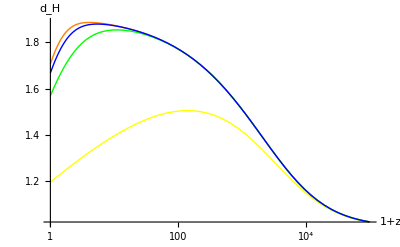

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000355015}. NIntegrate obtained -0.000783777 + 0.0364855\ ⅈ and 0.000284975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0000873015}. NIntegrate obtained -0.000300371 + 0.0185285\ ⅈ and 0.0000735108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000355015}. NIntegrate obtained -0.00384154 + 0.0349162\ ⅈ and 0.000284883 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

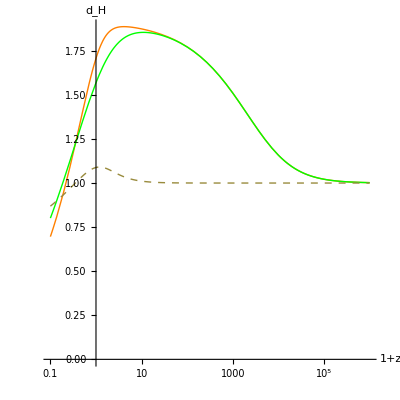

```mathematica
(*********************************************)
Print[Style["Plot Hubble distances",30,Bold,Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn]},{mn,1,10^5},PlotStyle->{Orange,Yellow,Green,Blue},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^6},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"},AxesOrigin-> {1,0},AspectRatio->1]
```

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.43433} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

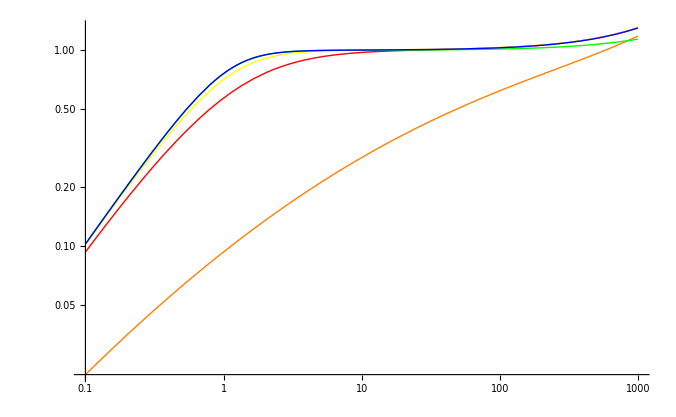

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434321} lies outside the range of data in the interpolating function. Extrapolation will be used.

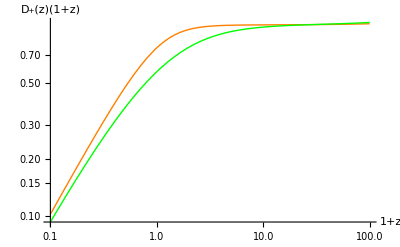

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",30,Bold,Orange]]
(*********************************************)
(*
GS1:=mn;
GL1:=0.7600404258603178*mn;
G21:=0.30903531541715085 mn;
G31:=0.5128033128651972 mn;
G41:=0.667848857875413 mn;
*)
LogLogPlot[{mn GrowthDE3[1/mn],mn GrowthDE2[1/mn],mn GrowthDE4[1/mn],mn GrowthL[1/mn],mn GrowthL2[1/mn]},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
(*
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
*)
(*
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4},PlotRange->{0.1,100}]
*)
LogLogPlot[{(mn)GrowthL[1/mn],(mn)GrowthDE3[1/mn]},{mn,0.1,100},PlotStyle->{Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"LCDM","DE3"},LegendPosition->{1.1,-0.4}]
(*
LogLogPlot[{Piecewise[{{(mn)GL[mn],mn≥1},{0.7600404258603178*mn,mn<1}}],Piecewise[{{(mn)GDE3[mn],mn≥1},{0.5128033128651972 *mn,mn<1}}]},{mn,0.1,100}]
*)
(*

LogLogPlot[{Piecewise[{(mn)GL[mn],mn≥1},{0.7600404258603178*mn,mn<1}],Piecewise[{(mn)GDE3[mn],mn≥1},{0.5128033128651972 *mn,mn<1}]},{mn,0.1,100},PlotStyle->{Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"LCDM","DE3"},LegendPosition->{1.1,-0.4}]


LogLogPlot[{Piecewise[{(mn)GS[mn],mn≥1},{mn,mn<1}],Piecewise[{(mn)GL[mn]},{0.7600404258603178*mn,mn<1}],Piecewise[{(mn)G2[mn]},{0.30903531541715085 mn,mn<1}],Piecewise[{(mn)G3[mn]},{0.5128033128651972 mn,mn<1}],Piecewise[{(mn)G4[mn]},{0.667848857875413 mn,mn<1}]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
LogLogPlot[{Piecewise[{(mn)GL[mn]},{0.7600404258603178*mn,mn<1}],Piecewise[{(mn)G3f[mn]},{0.5128033128651972 mn,mn<1}]},{mn,0.1,100},PlotStyle->{Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"LCDM","DE3"},LegendPosition->{1.1,-0.4}]
(*Another normalization*)
LogLogPlot[{GS[mn]/GS[mn],GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)/(D_+)^s(z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
(*LogLogPlot[{1,GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]*)

*)
```

Import power spectrum of LCDM calculated by cmbeasy, and some test

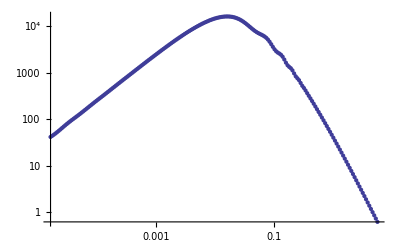

0.0000167287

0.000112794

281.02

201

0.0000118774==71. √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",30,Bold,Orange]]
(*********************************************)
PowerS=Import["cdm_11-27.dat"];
ListLogLogPlot[PowerS]
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",30,Bold,Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

100.004

52734.3

1.87323×10^6

1.03875×10^8

9.1433×10^9

9.00944×10^11

```mathematica
aokTabs11=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,1,leth}];
aokTabL11=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,1,leth}];
aokTabDE211=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,1,leth}];
aokTabDE311=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,1,leth}];
aokTabDE411=Table[a4/.FindRoot[PowerS[[i,1]]==kDE4[a4],{a4,0.0001}],{i,1,leth}];
Export["DEs\\Sync3\\aokTabs11.xls",aokTabs11,"XLS"]
Export["DEs\\Sync3\\aokTabL11.xls",aokTabL11,"XLS"]
Export["DEs\\Sync3\\aokTabDE211.xls",aokTabDE211,"XLS"]
Export["DEs\\Sync3\\aokTabDE311.xls",aokTabDE311,"XLS"]
Export["DEs\\Sync3\\aokTabDE411.xls",aokTabDE411,"XLS"]
```

DEs\Sync3\aokTabs11.xls

DEs\Sync3\aokTabL11.xls

DEs\Sync3\aokTabDE211.xls

DEs\Sync3\aokTabDE311.xls

DEs\Sync3\aokTabDE411.xls

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",30,Bold,Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
(*PowerS[[100]][[1]]== HL[L]
Solve[(PowerS[[115]][[1]])^2 L^4== L^4(HL[L])^2,L]
LogLogPlot[{L^4(Hs[L])^2,L^4(HL[L])^2,L^4(H2[L])^2,L^4(H3[L])^2,L^4(H4[L])^2,(PowerS[[115]][[1]])^2 L^4},{L,0.00001,100000},PlotStyle->{Red,Orange,Yellow,Green,Blue,Black}]*)
aokTabs=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,tranzs+1,leth}];
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,tranzL+1,leth}];
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,tranzDE2+1,leth}];
aokTabDE3=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,tranzDE3+1,leth}];
aokTabDE4=Table[a4/.FindRoot[PowerS[[i,1]]==kDE4[a4],{a4,0.0001}],{i,tranzDE4+1,leth}];
(*Check the results*)
aokTabs[[1]]
Length[aokTabL]
Length[aokTabs]
Length[aokTabDE2]
Length[aokTabDE3]
Length[aokTabDE4]
aokTabs
aokTabL
aokTabDE2
aokTabDE3
aokTabDE4
```

Create tables for power spectrums, and test

0.995573

178

170

172

178

178

{0.995573,0.954356,0.914848,0.876979,0.840679,0.805884,0.772532,0.740562,0.709917,0.680543,0.652386,0.625396,0.599525,0.574726,0.550954,0.528168,0.506326,0.485389,0.46532,0.446082,0.427642,0.409965,0.39302,0.376778,0.361208,0.346283,0.331977,0.318263,0.305117,0.292515,0.280435,0.268856,0.257755,0.247115,0.236915,0.227137,0.217764,0.208779,0.200166,0.191909,0.183994,0.176406,0.169133,0.16216,0.155476,0.149068,0.142926,0.137037,0.131392,0.125981,0.120793,0.11582,0.111052,0.106482,0.1021,0.0978995,0.0938726,0.0900121,0.0863111,0.082763,0.0793615,0.0761005,0.0729742,0.069977,0.0671035,0.0643487,0.0617076,0.0591756,0.056748,0.0544206,0.0521893,0.05005,0.0479989,0.0460324,0.0441471,0.0423395,0.0406064,0.0389447,0.0373515,0.035824,0.0343594,0.0329551,0.0316087,0.0303177,0.0290799,0.027893,0.026755,0.0256638,0.0246175,0.0236143,0.0226523,0.0217298,0.0208453,0.0199971,0.0191838,0.0184039,0.017656,0.0169389,0.0162512,0.0155917,0.0149592,0.0143528,0.0137711,0.0132134,0.0126785,0.0121655,0.0116735,0.0112017,0.0107492,0.0103152,0.00989903,0.00949985,0.00911698,0.00874977,0.00839757,0.00805976,0.00773574,0.00742495,0.00712685,0.00684091,0.00656663,0.00630353,0.00605115,0.00580906,0.00557682,0.00535404,0.00514032,0.00493529,0.00473859,0.00454989,0.00436885,0.00419516,0.00402852,0.00386864,0.00371524,0.00356805,0.00342683,0.00329132,0.00316129,0.00303652,0.00291679,0.00280189,0.00269164,0.00258583,0.00248429,0.00238683,0.0022933,0.00220354,0.00211738,0.00203469,0.00195532,0.00187913,0.001806,0.0017358,0.00166841,0.00160371,0.0015416,0.00148198,0.00142473,0.00136977,0.001317,0.00126633,0.00121767,0.00117095,0.00112609,0.001083,0.00104162,0.00100188,0.000963719,0.000927061}

{0.975311,0.929032,0.885366,0.844138,0.805184,0.76835,0.733496,0.700488,0.669206,0.639534,0.61137,0.584615,0.559182,0.534987,0.511955,0.490017,0.469109,0.449169,0.430145,0.411986,0.394644,0.378076,0.362241,0.347103,0.332627,0.318779,0.305529,0.292848,0.28071,0.269089,0.257962,0.247306,0.237099,0.227322,0.217956,0.208982,0.200383,0.192144,0.184248,0.176681,0.169429,0.162477,0.155815,0.149428,0.143306,0.137438,0.131812,0.126419,0.121249,0.116292,0.11154,0.106984,0.102616,0.0984279,0.0944124,0.0905623,0.0868708,0.0833312,0.0799373,0.076683,0.0735626,0.0705705,0.0677013,0.06495,0.0623118,0.0597819,0.0573559,0.0550294,0.0527984,0.050659,0.0486072,0.0466396,0.0447526,0.042943,0.0412074,0.0395429,0.0379466,0.0364156,0.0349472,0.0335389,0.0321881,0.0308926,0.02965,0.0284581,0.0273149,0.0262184,0.0251665,0.0241576,0.0231898,0.0222615,0.0213709,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154343,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990339,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781,0.00779086,0.00748665,0.00719466,0.00691438,0.00664533,0.00638707,0.00613915,0.00590115,0.00567266,0.0054533,0.00524269,0.00504049,0.00484634,0.00465992,0.00448092,0.00430903,0.00414396,0.00398545,0.00383322,0.00368701,0.00354659,0.00341172,0.00328218,0.00315774,0.00303821,0.00292338,0.00281306,0.00270708,0.00260525,0.00250742,0.00241341,0.00232308,0.00223627,0.00215285,0.00207268,0.00199563,0.00192157,0.00185038,0.00178195,0.00171617,0.00165293,0.00159213,0.00153367,0.00147746,0.00142341,0.00137143,0.00132145,0.00127337,0.00122713,0.00118266,0.00113987,0.00109871,0.00105912,0.00102102,0.000984362,0.000949088,0.000915142,0.000882474,0.000851032,0.000820768,0.000791636,0.000763591,0.000736592}

{0.961053,0.91905,0.878899,0.840518,0.80383,0.768758,0.73523,0.703179,0.672539,0.643247,0.615243,0.58847,0.562874,0.538403,0.515006,0.492636,0.471248,0.450799,0.431246,0.41255,0.394673,0.377579,0.361233,0.345603,0.330657,0.316364,0.302696,0.289625,0.277125,0.26517,0.253738,0.242804,0.232346,0.222345,0.212779,0.20363,0.194879,0.186508,0.178502,0.170844,0.163518,0.156511,0.149808,0.143395,0.137261,0.131393,0.125779,0.120408,0.11527,0.110354,0.10565,0.10115,0.0968445,0.0927248,0.0887829,0.0850111,0.0814019,0.0779483,0.0746435,0.071481,0.0684546,0.0655583,0.0627866,0.0601339,0.0575952,0.0551654,0.0528399,0.0506141,0.0484836,0.0464445,0.0444926,0.0426242,0.0408356,0.0391236,0.0374846,0.0359156,0.0344135,0.0329754,0.0315987,0.0302805,0.0290185,0.0278101,0.0266531,0.0255452,0.0244843,0.0234685,0.0224957,0.0215642,0.020672,0.0198177,0.0189994,0.0182158,0.0174652,0.0167463,0.0160577,0.0153981,0.0147663,0.014161,0.0135813,0.0130258,0.0124937,0.0119839,0.0114955,0.0110276,0.0105792,0.0101496,0.0097379,0.00934342,0.00896539,0.00860312,0.00825594,0.0079232,0.00760429,0.00729863,0.00700566,0.00672483,0.00645564,0.00619758,0.0059502,0.00571303,0.00548565,0.00526764,0.00505862,0.00485819,0.004666,0.0044817,0.00430495,0.00413545,0.00397289,0.00381697,0.00366742,0.00352397,0.00338636,0.00325435,0.00312771,0.0030062,0.00288963,0.00277777,0.00267044,0.00256744,0.00246859,0.00237373,0.00228269,0.0021953,0.00211142,0.00203089,0.00195359,0.00187938,0.00180813,0.00173971,0.00167402,0.00161093,0.00155034,0.00149215,0.00143626,0.00138258,0.00133101,0.00128147,0.00123387,0.00118814,0.00114419,0.00110196,0.00106138,0.00102237,0.000984884,0.000948847,0.000914203,0.000880897,0.000848875,0.000818083,0.000788473,0.000759998}

{1.04018,0.991235,0.944786,0.900699,0.858844,0.819099,0.781348,0.745483,0.7114,0.679004,0.648204,0.618913,0.591052,0.564542,0.539313,0.515297,0.49243,0.470652,0.449906,0.430137,0.411297,0.393336,0.376211,0.359878,0.344297,0.329431,0.315244,0.301702,0.288773,0.276427,0.264636,0.253372,0.24261,0.232326,0.222498,0.213102,0.20412,0.195531,0.187317,0.179461,0.171946,0.164757,0.157878,0.151295,0.144996,0.138966,0.133194,0.127668,0.122378,0.117313,0.112463,0.107818,0.103369,0.0991085,0.0950272,0.0911177,0.0873724,0.0837843,0.0803465,0.0770525,0.0738962,0.0708717,0.0679733,0.0651957,0.0625336,0.0599821,0.0575367,0.0551926,0.0529458,0.050792,0.0487273,0.046748,0.0448505,0.0430313,0.0412872,0.039615,0.0380117,0.0364743,0.0350002,0.0335868,0.0322314,0.0309316,0.0296852,0.0284899,0.0273437,0.0262443,0.02519,0.0241788,0.023209,0.0222788,0.0213865,0.0205308,0.0197099,0.0189225,0.0181672,0.0174426,0.0167476,0.0160808,0.0154412,0.0148275,0.0142388,0.0136739,0.013132,0.012612,0.0121132,0.0116345,0.0111752,0.0107344,0.0103115,0.00990566,0.0095162,0.00914246,0.00878378,0.00843955,0.00810918,0.00779211,0.00748777,0.00719567,0.00691529,0.00664616,0.00638782,0.00613983,0.00590176,0.00567322,0.0054538,0.00524315,0.0050409,0.00484671,0.00466026,0.00448122,0.0043093,0.00414421,0.00398567,0.00383342,0.0036872,0.00354676,0.00341187,0.00328231,0.00315786,0.00303832,0.00292348,0.00281315,0.00270716,0.00260533,0.00250748,0.00241347,0.00232313,0.00223632,0.0021529,0.00207272,0.00199566,0.0019216,0.00185041,0.00178198,0.00171619,0.00165295,0.00159215,0.00153369,0.00147748,0.00142343,0.00137145,0.00132146,0.00127338,0.00122714,0.00118267,0.00113988,0.00109872,0.00105912,0.00102103,0.000984367,0.000949093,0.000915147,0.000882478,0.000851035,0.000820771,0.000791639,0.000763594,0.000736595}

{0.992985,0.945881,0.901343,0.859211,0.819337,0.781579,0.745808,0.7119,0.679742,0.649226,0.620255,0.592733,0.566577,0.541704,0.51804,0.495514,0.474063,0.453625,0.434144,0.415567,0.397846,0.380934,0.364788,0.34937,0.334641,0.320566,0.307113,0.294251,0.281951,0.270186,0.25893,0.24816,0.237852,0.227986,0.21854,0.209496,0.200835,0.192541,0.184597,0.176987,0.169697,0.162713,0.156021,0.149609,0.143465,0.137577,0.131934,0.126526,0.121342,0.116374,0.111612,0.107047,0.102671,0.0984757,0.0944542,0.0905989,0.0869027,0.0833591,0.0799617,0.0767043,0.0735812,0.0705867,0.0677155,0.0649624,0.0623226,0.0597914,0.0573641,0.0550366,0.0528047,0.0506644,0.048612,0.0466438,0.0447563,0.0429461,0.0412102,0.0395454,0.0379487,0.0364174,0.0349488,0.0335403,0.0321894,0.0308937,0.0296509,0.0284589,0.0273156,0.026219,0.0251671,0.0241581,0.0231902,0.0222618,0.0213713,0.0205169,0.0196974,0.0189112,0.018157,0.0174334,0.0167393,0.0160733,0.0154344,0.0148213,0.0142332,0.0136689,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107317,0.010309,0.00990341,0.00951417,0.00914062,0.00878212,0.00843805,0.00810782,0.00779087,0.00748666,0.00719466,0.00691438,0.00664534,0.00638708,0.00613916,0.00590115,0.00567266,0.0054533,0.0052427,0.00504049,0.00484634,0.00465992,0.00448092,0.00430903,0.00414397,0.00398545,0.00383322,0.00368701,0.00354659,0.00341172,0.00328218,0.00315774,0.00303821,0.00292338,0.00281306,0.00270708,0.00260525,0.00250742,0.00241341,0.00232308,0.00223627,0.00215285,0.00207268,0.00199563,0.00192157,0.00185038,0.00178195,0.00171617,0.00165293,0.00159213,0.00153367,0.00147746,0.00142341,0.00137143,0.00132145,0.00127337,0.00122713,0.00118266,0.00113987,0.00109871,0.00105912,0.00102102,0.000984362,0.000949088,0.000915143,0.000882474,0.000851032,0.000820768,0.000791636,0.000763591,0.000736592}

```mathematica
(*********************************************)
Print[Style["Export aok table",30,Bold,Orange]]
(*********************************************)
Export["DEs\\Sync3\\aokTabs.xls",aokTabs,"XLS"]
Export["DEs\\Sync3\\aokTabL.xls",aokTabL,"XLS"]
Export["DEs\\Sync3\\aokTabDE2.xls",aokTabDE2,"XLS"]
Export["DEs\\Sync3\\aokTabDE3.xls",aokTabDE3,"XLS"]
Export["DEs\\Sync3\\aokTabDE4.xls",aokTabDE4,"XLS"]
```

Export aok table

DEs\Sync3\aokTabs.xls

DEs\Sync3\aokTabL.xls

DEs\Sync3\aokTabDE2.xls

DEs\Sync3\aokTabDE3.xls

DEs\Sync3\aokTabDE4.xls

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",30,Bold,Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
fracs=1/((Growths[1]/Growths[1/aokTabs[[norts]]])/(GrowthL[1]/GrowthL[1/aokTabL[[norts]]]))
frac2=1/((GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[nort2]]])/(GrowthL[1]/GrowthL[1/aokTabL[[nort2]]]))
frac3=1/((GrowthDE3[1]/GrowthDE3[1/aokTabDE3[[nort3]]])/(GrowthL[1]/GrowthL[1/aokTabL[[nort3]]]))
frac4=1/((GrowthDE4[1]/GrowthDE4[1/aokTabDE4[[nort4]]])/(GrowthL[1]/GrowthL[1/aokTabL[[nort4]]]))
(*
fracs=1/((Growths[1]/Growths[aokTabs[[norts]]])/(GrowthL[1]/GrowthL[aokTabL[[norts]]]))
frac2=1/((GrowthDE2[1]/GrowthDE2[aokTabDE2[[nort2]]])/(GrowthL[1]/GrowthL[aokTabL[[nort2]]]))
frac3=1/((GrowthDE3[1]/GrowthDE3[aokTabDE3[[nort3]]])/(GrowthL[1]/GrowthL[aokTabL[[nort3]]]))
frac4=1/((GrowthDE4[1]/GrowthDE4[aokTabDE4[[nort4]]])/(GrowthL[1]/GrowthL[aokTabL[[nort4]]]))
*)
(*frac2=1;frac3=1;frac4=1;*)
```

Normalization factors. normalized to a early time of about a=10^-3

764.387

4.62187

1.27963

1.06654

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",30,Bold,Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE2}];
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE3[1/aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE3}];
Qfactor4=Table[{PowerS[[i+tranzDE4,1]],frac4 (GrowthDE4[1]/GrowthDE4[1/aokTabDE4[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE4}];
(*
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE2}];
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE3}];
Qfactor4=Table[{PowerS[[i+tranzDE4,1]],frac4 (GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE4}];
*)
Qfactor2Ex=Table[{PowerS[[i,1]],frac2},{i,1,tranzDE2}];
Qfactor3Ex=Table[{PowerS[[i,1]],frac3},{i,1,tranzDE3}];
Qfactor4Ex=Table[{PowerS[[i,1]],frac4},{i,1,tranzDE4}];
Qfac2=Join[Qfactor2Ex,Qfactor2];
Qfac3=Join[Qfactor3Ex,Qfactor3];
Qfac4=Join[Qfactor4Ex,Qfactor4];
Qfactor2[[1]]
Qfactor2[[1]][[1]]
(*********************************************)
Print[Style["Export the Q factors",30,Bold,Orange]]
(*********************************************)
Export["DEs\\Sync3\\QfactorDE2vsL.xls",Qfac2,"XLS"]
Export["DEs\\Sync3\\QfactorDE3vsL.xls",Qfac3,"XLS"]
Export["DEs\\Sync3\\QfactorDE4vsL.xls",Qfac4,"XLS"]
```

Tables for Q factors

{0.000105842,4.59551}

0.000105842

Export the Q factors

DEs\Sync3\QfactorDE2vsL.xls

DEs\Sync3\QfactorDE3vsL.xls

DEs\Sync3\QfactorDE4vsL.xls

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",30,Bold,Orange]]
(*********************************************)
(*
PowerSDE2=Table[{PowerS[[i,1]]/h,(frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE2}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(frac3 (GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE3}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(frac4 (GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE4}];
*)
 (*It should be faster but the expression sucks.*)
(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",30,Bold,Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]],PowerS[[i,2]]},{i,1,leth}];
PowerSDE2=Table[{PowerSS[[i,1]],(Qfac2[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE3=Table[{PowerSS[[i,1]],(Qfac3[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE4=Table[{PowerSS[[i,1]],(Qfac4[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
ListLogLogPlot[PowerS]
ListLogLogPlot[PowerSS]
(*********************************************)
Print[Style["Export power spectrum raw data",30,Bold,Orange]]
(*********************************************)
Export["DEs\\Sync3\\PowerSScale.xls",PowerSS,"XLS"]
Export["DEs\\Sync3\\PowerSDE2.xls",PowerSDE2,"XLS"]
Export["DEs\\Sync3\\PowerSDE3.xls",PowerSDE3,"XLS"]
Export["DEs\\Sync3\\PowerSDE4.xls",PowerSDE4,"XLS"]
```

Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.

Construct the normalized power spectrum (different units) and export them

-Graphics-

-Graphics-

Export power spectrum raw data

DEs\Sync3\PowerSScale.xls

DEs\Sync3\PowerSDE2.xls

DEs\Sync3\PowerSDE3.xls

DEs\Sync3\PowerSDE4.xls

Import the Q factors calculated previously.

Plot P(k)

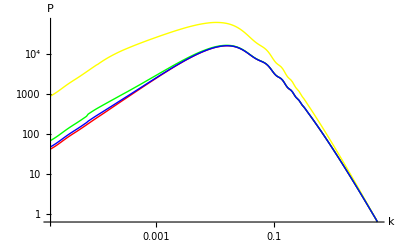

-Graphics-

Plot Qfactors vs k

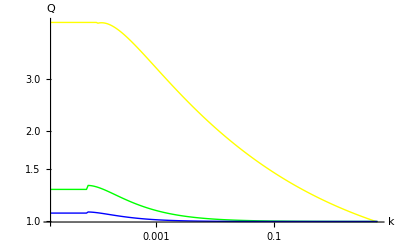

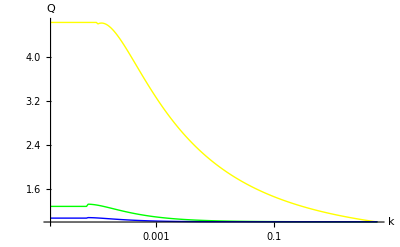

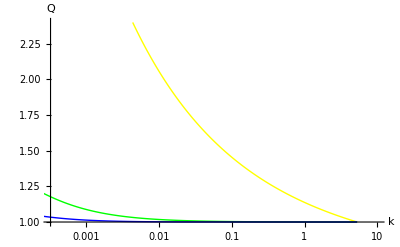

```mathematica
(*********************************************)
Print[Style["Import the Q factors calculated previously.",30,Bold,Orange]]
(*********************************************)
QfDe2VsL=Import["DEs\\Sync3\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["DEs\\Sync3\\QfactorDE3vsL.xls"];
QfDe4VsL=Import["DEs\\Sync3\\QfactorDE4vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3,PowerSDE4},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Yellow,Green,Blue},PlotLegend->{"LCDM","w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3,PowerSDE4},Joined->True, AxesLabel-> {k,P},PlotRange->Automatic,PlotStyle->{Red,Yellow,Green,Blue},PlotLegend->{"LCDM","w2","w3","w4"},LegendPosition->{1.1,-0.4}]
(*********************************************)
Print[Style["Plot Qfactors vs k",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->{{3.3*10^-4,10},{1,2.4}},PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
```